```mathematica
Import["/home/jadeleon/Documents/component-erasing-maps/mathematica/quantumJA.m"]
```

# Operaciones PCE

El nombre PCE deviene del nombre de estas operaciones en inglés: Pauli-component-erasing operations.

```mathematica
Log[4,16]
```

2

## 1 qubit

La matriz de densidad de 1 qubit, en la base de Pauli, se escribe como 
                                             ρ=1/2(ℐ+∑_i r_i σ_i)

Una operación PCE ℰ hace la transformación r_i⟶τ_i r_i, donde τ_i=0,1. Entonces el superoperador ℰ es diagonal en la base de Pauli:
                                        ℰ = (1 | 0 | 0 | 0
0 | τ_1 | 0 | 0
0 | 0 | τ_2 | 0
0 | 0 | 0 | τ_3)
Para que ℰ sea un canal cuántico, debe ser:
(1) mapeo afín de matrices de densidad.
(2) completamente positivo (CP).

La condición (1) es fácil de ver que se cumple, pero la condición (2) no.
Para evaluar si ℰ es CP, hay que hacer un cambio de base a la base computacional, calcular la matriz de Choi ℰ^R y evaluar si es positiva semidefinida.

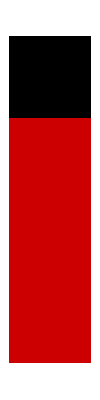
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
oneQDiag=ToExpression[Import["/home/jadeleon/Documents/component-erasing-maps/results/OneQubit.txt","List"]];ReducedTwoQBoard[{#},2]&/@oneQDiag
```

#### Estos dibujos tienen otra interpretación...

```mathematica
$Assumptions=True;
Subscript[τ, 0]=1;
4 #≥0&/@(PCE[Table[Subscript[τ, i],{i,0,3}]//Flatten]//Reshuffle//Eigenvalues)//TableForm
```

1+τ_1-τ_2-τ_3≥0
1-τ_1-τ_2+τ_3≥0
1-τ_1+τ_2-τ_3≥0
1+τ_1+τ_2+τ_3≥0

Fujiwara-Algoet. (revisar)

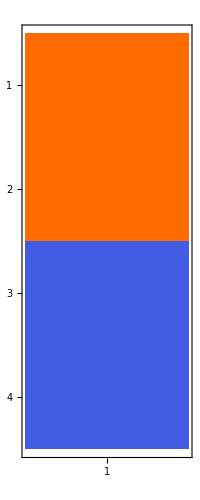
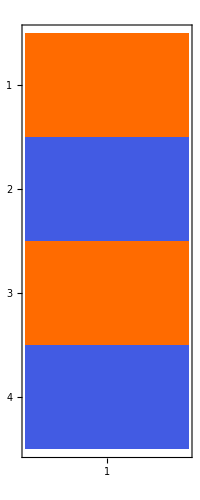
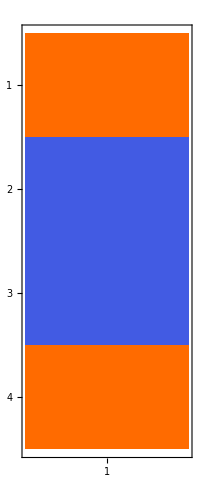
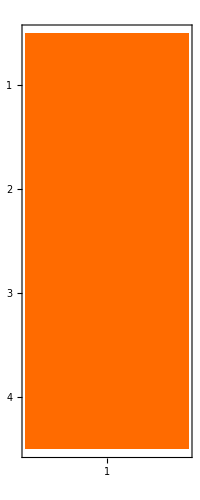

```mathematica
$Assumptions=And@@Table[Subscript[r, i]==1,{i,0,3}];
Subscript[r, 0]=1;
(ArrayReshape[If[FullSimplify[#>0],1,-1]&/@List@@Expand[#],{4,1}]//MatrixPlot)&/@({1/4 (Subscript[r, 0]+Subscript[r, 1]-Subscript[r, 2]-Subscript[r, 3]),1/4 (Subscript[r, 0]-Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 3]),1/4 (Subscript[r, 0]-Subscript[r, 1]-Subscript[r, 2]+Subscript[r, 3]),1/4 (Subscript[r, 0]+Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 3])})
```

Cada uno de los dibujos ahora representa cada una de las 4 desigualdades que debe de cumplir la operación PCE para ser un canal cuántico. 

La cantidad de cuadros naranjas y azules es equivalente a que el lado izquierdo de las desigualdades sean iguales a cero. 

Más cuadros naranjas que azules representa que el lado izquierdo de la desigualdad es mayor a cero.

## 2 qubits

Para 2 qubits, la matriz de densidad en la base de Pauli se escribe como 
                                        ρ=1/4(∑_i r_(i, j)σ_i⊗σ_j)
Una operación PCE ℰ hace la transformación r_(i, j)⟶τ_(i, j)r_(i, j), donde τ_(i, j)=0,1.

```mathematica
Subscript[τ, 0,0]=1;DiagonalMatrix[Flatten[Table[Subscript[τ, i,j],{i,0,3},{j,0,3}]]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | τ_(0,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | τ_(0,2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | τ_(0,3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | τ_(1,0) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | τ_(1,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | τ_(1,2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | τ_(1,3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | τ_(2,0) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | τ_(2,1) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | τ_(2,2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | τ_(2,3) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | τ_(3,0) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | τ_(3,1) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | τ_(3,2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | τ_(3,3))

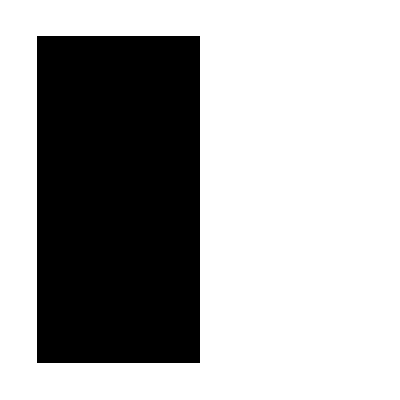
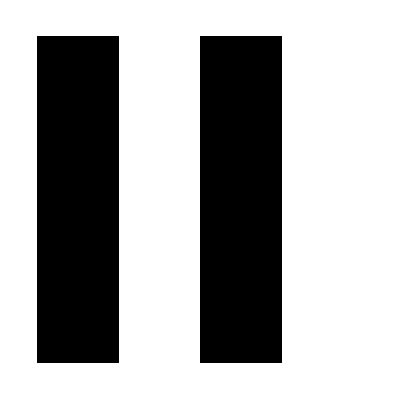
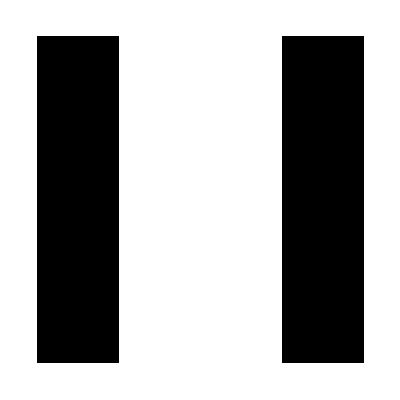
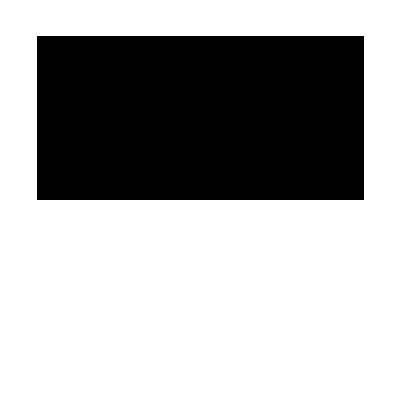
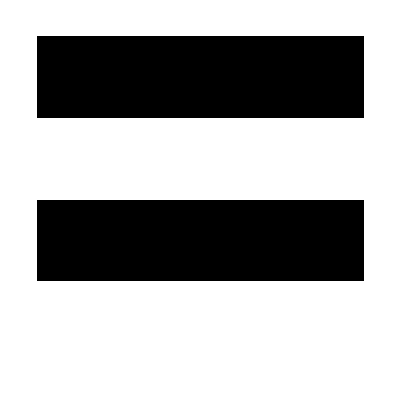
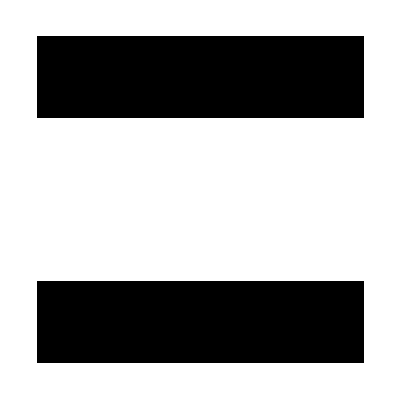
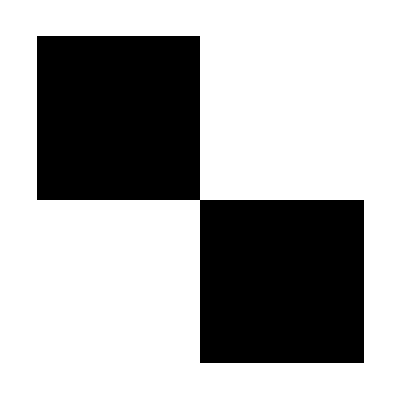
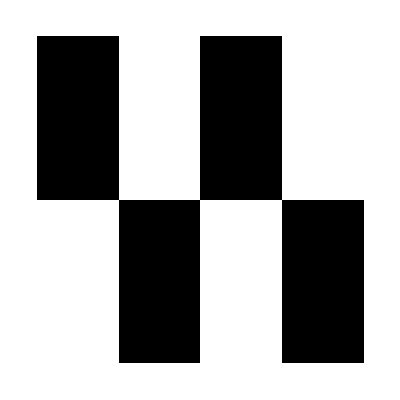


```mathematica
twoQDiag=ToExpression[Import["/home/jadeleon/Documents/component-erasing-maps/results/TwoQubits.txt","List"]];ArrayPlot/@ArrayReshape[twoQDiag,{67,4,4}][[67-15;;67]]
```

```mathematica
Subscript[τ, 0,0]=1;16#≥0&/@(PCE[Table[Subscript[τ, i,j],{i,0,3},{j,0,3}]//Flatten]//Reshuffle//Eigenvalues)//TableForm
```

1+τ_(0,1)+τ_(0,2)+τ_(0,3)+τ_(1,0)+τ_(1,1)+τ_(1,2)+τ_(1,3)-τ_(2,0)-τ_(2,1)-τ_(2,2)-τ_(2,3)-τ_(3,0)-τ_(3,1)-τ_(3,2)-τ_(3,3)≥0
1+τ_(0,1)+τ_(0,2)+τ_(0,3)-τ_(1,0)-τ_(1,1)-τ_(1,2)-τ_(1,3)+τ_(2,0)+τ_(2,1)+τ_(2,2)+τ_(2,3)-τ_(3,0)-τ_(3,1)-τ_(3,2)-τ_(3,3)≥0
1+τ_(0,1)-τ_(0,2)-τ_(0,3)+τ_(1,0)+τ_(1,1)-τ_(1,2)-τ_(1,3)+τ_(2,0)+τ_(2,1)-τ_(2,2)-τ_(2,3)+τ_(3,0)+τ_(3,1)-τ_(3,2)-τ_(3,3)≥0
1+τ_(0,1)-τ_(0,2)-τ_(0,3)-τ_(1,0)-τ_(1,1)+τ_(1,2)+τ_(1,3)-τ_(2,0)-τ_(2,1)+τ_(2,2)+τ_(2,3)+τ_(3,0)+τ_(3,1)-τ_(3,2)-τ_(3,3)≥0
1-τ_(0,1)+τ_(0,2)-τ_(0,3)+τ_(1,0)-τ_(1,1)+τ_(1,2)-τ_(1,3)-τ_(2,0)+τ_(2,1)-τ_(2,2)+τ_(2,3)-τ_(3,0)+τ_(3,1)-τ_(3,2)+τ_(3,3)≥0
1-τ_(0,1)+τ_(0,2)-τ_(0,3)-τ_(1,0)+τ_(1,1)-τ_(1,2)+τ_(1,3)+τ_(2,0)-τ_(2,1)+τ_(2,2)-τ_(2,3)-τ_(3,0)+τ_(3,1)-τ_(3,2)+τ_(3,3)≥0
1-τ_(0,1)-τ_(0,2)+τ_(0,3)+τ_(1,0)-τ_(1,1)-τ_(1,2)+τ_(1,3)+τ_(2,0)-τ_(2,1)-τ_(2,2)+τ_(2,3)+τ_(3,0)-τ_(3,1)-τ_(3,2)+τ_(3,3)≥0
1-τ_(0,1)-τ_(0,2)+τ_(0,3)-τ_(1,0)+τ_(1,1)+τ_(1,2)-τ_(1,3)-τ_(2,0)+τ_(2,1)+τ_(2,2)-τ_(2,3)+τ_(3,0)-τ_(3,1)-τ_(3,2)+τ_(3,3)≥0
1-τ_(0,1)-τ_(0,2)+τ_(0,3)-τ_(1,0)+τ_(1,1)+τ_(1,2)-τ_(1,3)+τ_(2,0)-τ_(2,1)-τ_(2,2)+τ_(2,3)-τ_(3,0)+τ_(3,1)+τ_(3,2)-τ_(3,3)≥0
1-τ_(0,1)-τ_(0,2)+τ_(0,3)+τ_(1,0)-τ_(1,1)-τ_(1,2)+τ_(1,3)-τ_(2,0)+τ_(2,1)+τ_(2,2)-τ_(2,3)-τ_(3,0)+τ_(3,1)+τ_(3,2)-τ_(3,3)≥0
1-τ_(0,1)+τ_(0,2)-τ_(0,3)-τ_(1,0)+τ_(1,1)-τ_(1,2)+τ_(1,3)-τ_(2,0)+τ_(2,1)-τ_(2,2)+τ_(2,3)+τ_(3,0)-τ_(3,1)+τ_(3,2)-τ_(3,3)≥0
1-τ_(0,1)+τ_(0,2)-τ_(0,3)+τ_(1,0)-τ_(1,1)+τ_(1,2)-τ_(1,3)+τ_(2,0)-τ_(2,1)+τ_(2,2)-τ_(2,3)+τ_(3,0)-τ_(3,1)+τ_(3,2)-τ_(3,3)≥0
1+τ_(0,1)-τ_(0,2)-τ_(0,3)-τ_(1,0)-τ_(1,1)+τ_(1,2)+τ_(1,3)+τ_(2,0)+τ_(2,1)-τ_(2,2)-τ_(2,3)-τ_(3,0)-τ_(3,1)+τ_(3,2)+τ_(3,3)≥0
1+τ_(0,1)-τ_(0,2)-τ_(0,3)+τ_(1,0)+τ_(1,1)-τ_(1,2)-τ_(1,3)-τ_(2,0)-τ_(2,1)+τ_(2,2)+τ_(2,3)-τ_(3,0)-τ_(3,1)+τ_(3,2)+τ_(3,3)≥0
1+τ_(0,1)+τ_(0,2)+τ_(0,3)-τ_(1,0)-τ_(1,1)-τ_(1,2)-τ_(1,3)-τ_(2,0)-τ_(2,1)-τ_(2,2)-τ_(2,3)+τ_(3,0)+τ_(3,1)+τ_(3,2)+τ_(3,3)≥0
1+τ_(0,1)+τ_(0,2)+τ_(0,3)+τ_(1,0)+τ_(1,1)+τ_(1,2)+τ_(1,3)+τ_(2,0)+τ_(2,1)+τ_(2,2)+τ_(2,3)+τ_(3,0)+τ_(3,1)+τ_(3,2)+τ_(3,3)≥0

```mathematica
eigen=16*{1/16 (1+Subscript[r, 0,1]+Subscript[r, 0,2]+Subscript[r, 0,3]+Subscript[r, 1,0]+Subscript[r, 1,1]+Subscript[r, 1,2]+Subscript[r, 1,3]-Subscript[r, 2,0]-Subscript[r, 2,1]-Subscript[r, 2,2]-Subscript[r, 2,3]-Subscript[r, 3,0]-Subscript[r, 3,1]-Subscript[r, 3,2]-Subscript[r, 3,3]),1/16 (1+Subscript[r, 0,1]+Subscript[r, 0,2]+Subscript[r, 0,3]-Subscript[r, 1,0]-Subscript[r, 1,1]-Subscript[r, 1,2]-Subscript[r, 1,3]+Subscript[r, 2,0]+Subscript[r, 2,1]+Subscript[r, 2,2]+Subscript[r, 2,3]-Subscript[r, 3,0]-Subscript[r, 3,1]-Subscript[r, 3,2]-Subscript[r, 3,3]),1/16 (1+Subscript[r, 0,1]-Subscript[r, 0,2]-Subscript[r, 0,3]+Subscript[r, 1,0]+Subscript[r, 1,1]-Subscript[r, 1,2]-Subscript[r, 1,3]+Subscript[r, 2,0]+Subscript[r, 2,1]-Subscript[r, 2,2]-Subscript[r, 2,3]+Subscript[r, 3,0]+Subscript[r, 3,1]-Subscript[r, 3,2]-Subscript[r, 3,3]),1/16 (1+Subscript[r, 0,1]-Subscript[r, 0,2]-Subscript[r, 0,3]-Subscript[r, 1,0]-Subscript[r, 1,1]+Subscript[r, 1,2]+Subscript[r, 1,3]-Subscript[r, 2,0]-Subscript[r, 2,1]+Subscript[r, 2,2]+Subscript[r, 2,3]+Subscript[r, 3,0]+Subscript[r, 3,1]-Subscript[r, 3,2]-Subscript[r, 3,3]),1/16 (1-Subscript[r, 0,1]+Subscript[r, 0,2]-Subscript[r, 0,3]+Subscript[r, 1,0]-Subscript[r, 1,1]+Subscript[r, 1,2]-Subscript[r, 1,3]-Subscript[r, 2,0]+Subscript[r, 2,1]-Subscript[r, 2,2]+Subscript[r, 2,3]-Subscript[r, 3,0]+Subscript[r, 3,1]-Subscript[r, 3,2]+Subscript[r, 3,3]),1/16 (1-Subscript[r, 0,1]+Subscript[r, 0,2]-Subscript[r, 0,3]-Subscript[r, 1,0]+Subscript[r, 1,1]-Subscript[r, 1,2]+Subscript[r, 1,3]+Subscript[r, 2,0]-Subscript[r, 2,1]+Subscript[r, 2,2]-Subscript[r, 2,3]-Subscript[r, 3,0]+Subscript[r, 3,1]-Subscript[r, 3,2]+Subscript[r, 3,3]),1/16 (1-Subscript[r, 0,1]-Subscript[r, 0,2]+Subscript[r, 0,3]+Subscript[r, 1,0]-Subscript[r, 1,1]-Subscript[r, 1,2]+Subscript[r, 1,3]+Subscript[r, 2,0]-Subscript[r, 2,1]-Subscript[r, 2,2]+Subscript[r, 2,3]+Subscript[r, 3,0]-Subscript[r, 3,1]-Subscript[r, 3,2]+Subscript[r, 3,3]),1/16 (1-Subscript[r, 0,1]-Subscript[r, 0,2]+Subscript[r, 0,3]-Subscript[r, 1,0]+Subscript[r, 1,1]+Subscript[r, 1,2]-Subscript[r, 1,3]-Subscript[r, 2,0]+Subscript[r, 2,1]+Subscript[r, 2,2]-Subscript[r, 2,3]+Subscript[r, 3,0]-Subscript[r, 3,1]-Subscript[r, 3,2]+Subscript[r, 3,3]),1/16 (1-Subscript[r, 0,1]-Subscript[r, 0,2]+Subscript[r, 0,3]-Subscript[r, 1,0]+Subscript[r, 1,1]+Subscript[r, 1,2]-Subscript[r, 1,3]+Subscript[r, 2,0]-Subscript[r, 2,1]-Subscript[r, 2,2]+Subscript[r, 2,3]-Subscript[r, 3,0]+Subscript[r, 3,1]+Subscript[r, 3,2]-Subscript[r, 3,3]),1/16 (1-Subscript[r, 0,1]-Subscript[r, 0,2]+Subscript[r, 0,3]+Subscript[r, 1,0]-Subscript[r, 1,1]-Subscript[r, 1,2]+Subscript[r, 1,3]-Subscript[r, 2,0]+Subscript[r, 2,1]+Subscript[r, 2,2]-Subscript[r, 2,3]-Subscript[r, 3,0]+Subscript[r, 3,1]+Subscript[r, 3,2]-Subscript[r, 3,3]),1/16 (1-Subscript[r, 0,1]+Subscript[r, 0,2]-Subscript[r, 0,3]-Subscript[r, 1,0]+Subscript[r, 1,1]-Subscript[r, 1,2]+Subscript[r, 1,3]-Subscript[r, 2,0]+Subscript[r, 2,1]-Subscript[r, 2,2]+Subscript[r, 2,3]+Subscript[r, 3,0]-Subscript[r, 3,1]+Subscript[r, 3,2]-Subscript[r, 3,3]),1/16 (1-Subscript[r, 0,1]+Subscript[r, 0,2]-Subscript[r, 0,3]+Subscript[r, 1,0]-Subscript[r, 1,1]+Subscript[r, 1,2]-Subscript[r, 1,3]+Subscript[r, 2,0]-Subscript[r, 2,1]+Subscript[r, 2,2]-Subscript[r, 2,3]+Subscript[r, 3,0]-Subscript[r, 3,1]+Subscript[r, 3,2]-Subscript[r, 3,3]),1/16 (1+Subscript[r, 0,1]-Subscript[r, 0,2]-Subscript[r, 0,3]-Subscript[r, 1,0]-Subscript[r, 1,1]+Subscript[r, 1,2]+Subscript[r, 1,3]+Subscript[r, 2,0]+Subscript[r, 2,1]-Subscript[r, 2,2]-Subscript[r, 2,3]-Subscript[r, 3,0]-Subscript[r, 3,1]+Subscript[r, 3,2]+Subscript[r, 3,3]),1/16 (1+Subscript[r, 0,1]-Subscript[r, 0,2]-Subscript[r, 0,3]+Subscript[r, 1,0]+Subscript[r, 1,1]-Subscript[r, 1,2]-Subscript[r, 1,3]-Subscript[r, 2,0]-Subscript[r, 2,1]+Subscript[r, 2,2]+Subscript[r, 2,3]-Subscript[r, 3,0]-Subscript[r, 3,1]+Subscript[r, 3,2]+Subscript[r, 3,3]),1/16 (1+Subscript[r, 0,1]+Subscript[r, 0,2]+Subscript[r, 0,3]-Subscript[r, 1,0]-Subscript[r, 1,1]-Subscript[r, 1,2]-Subscript[r, 1,3]-Subscript[r, 2,0]-Subscript[r, 2,1]-Subscript[r, 2,2]-Subscript[r, 2,3]+Subscript[r, 3,0]+Subscript[r, 3,1]+Subscript[r, 3,2]+Subscript[r, 3,3]),1/16 (1+Subscript[r, 0,1]+Subscript[r, 0,2]+Subscript[r, 0,3]+Subscript[r, 1,0]+Subscript[r, 1,1]+Subscript[r, 1,2]+Subscript[r, 1,3]+Subscript[r, 2,0]+Subscript[r, 2,1]+Subscript[r, 2,2]+Subscript[r, 2,3]+Subscript[r, 3,0]+Subscript[r, 3,1]+Subscript[r, 3,2]+Subscript[r, 3,3])};
```

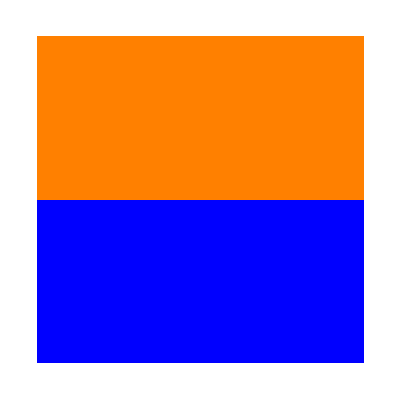
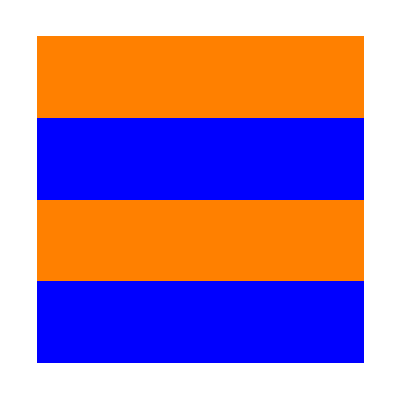
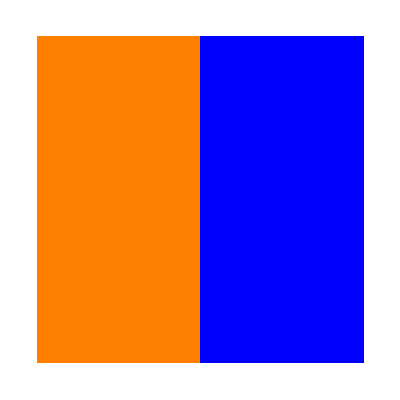
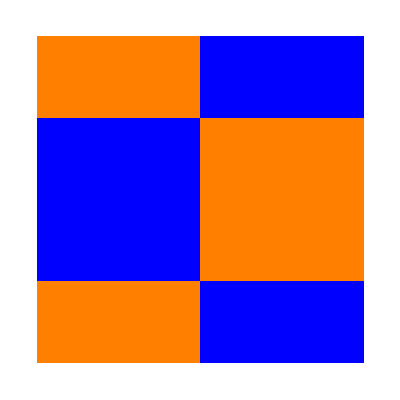
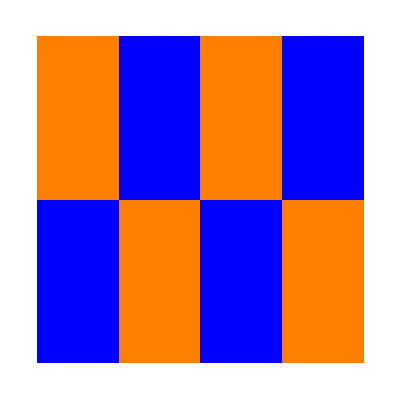
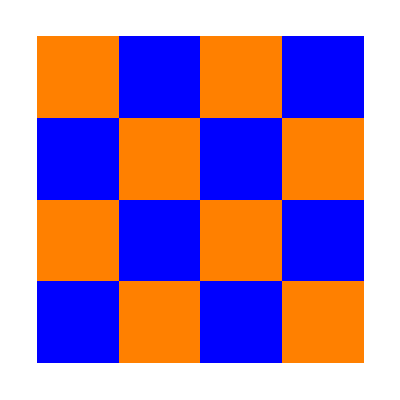
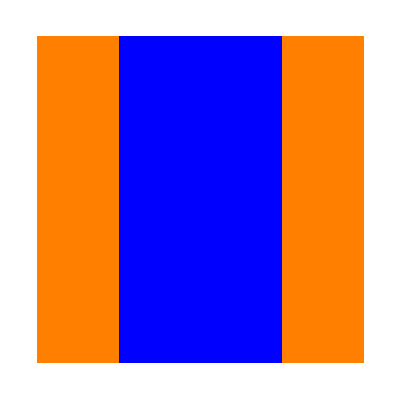
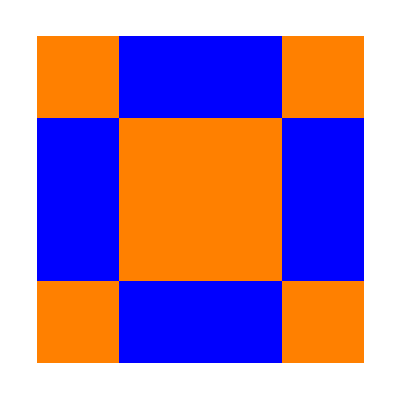

```mathematica
$Assumptions=And@@Flatten[{Table[Subscript[r, i,j]==2,{i,1,3},{j,0,3}],Table[Subscript[r, 0,j]==2,{j,1,3}]}];
(ArrayReshape[If[FullSimplify[#==1],Orange,If[FullSimplify[#==2],Orange,Blue]]&/@List@@Expand[#],{4,4}]//ArrayPlot)&/@eigen
```

```mathematica
c1=ArrayReshape[KroneckerProduct[{1,0,0,1},{1,1,0,0}],{4,4}]+ArrayReshape[KroneckerProduct[{0,1,1,0},{0,0,1,1}],{4,4}];
c2=ArrayReshape[KroneckerProduct[ConstantArray[1,{4,4}]-c1,{1,1,1,1}-{1,1,0,0}],{4,4,4}];
Cube3q[Position[ArrayReshape[KroneckerProduct[c1,{1,1,0,0}],{4,4,4}],1]-1]
Cube3q[Position[c2,1]-1]
Cube3q[Position[ArrayReshape[KroneckerProduct[c1,{1,1,0,0}],{4,4,4}]+c2,1]-1]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
PCE[Flatten[ArrayReshape[KroneckerProduct[c1,{1,1,0,0}],{4,4,4}]+c2]]//Reshuffle//Ptest
```

True

```mathematica
Cube3q[Position[ArrayReshape[KroneckerProduct[{1,1,0,0},{1,0,0,1},{1,1,1,1}],{4,4,4}]+ArrayReshape[KroneckerProduct[{1,1,1,1},{1,1,1,1}-{1,0,0,1},{1,1,1,1}-{1,1,0,0}],{4,4,4}],1]-1]
```

-Graphics3D-

```mathematica
q2c4V2=FindNextCase[a[[2;;]],4]//Length
```

29

```mathematica
qubit1={{1,1,1,1},{1,1,0,0},{1,0,1,0},{1,0,0,1}};
a=Flatten[Table[KroneckerProduct[{1,1,1,1}-qubit1[[i]],{1,1,1,1}-qubit1[[j]]]+KroneckerProduct[qubit1[[i]],qubit1[[j]]],{i,1,4},{j,1,4}],1];ArrayPlot[#]&/@a[[2;;]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

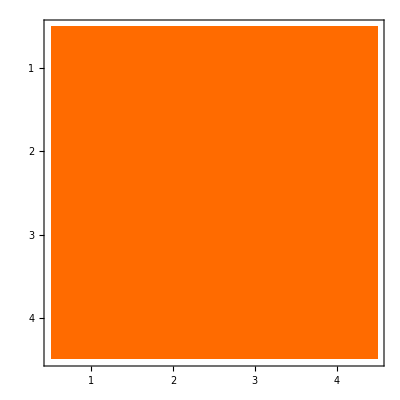
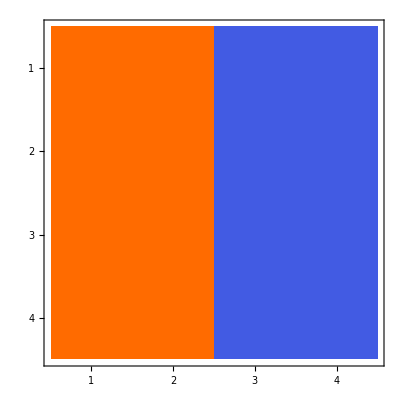
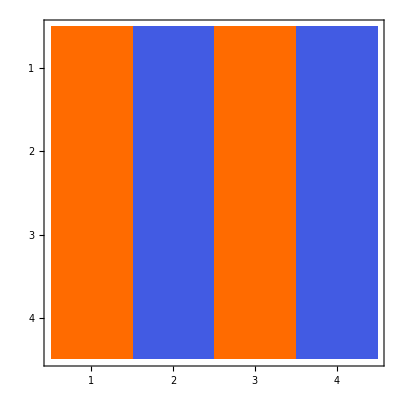
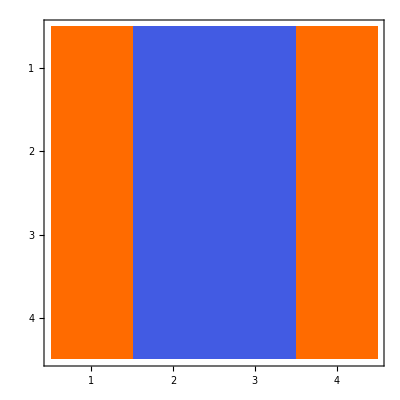
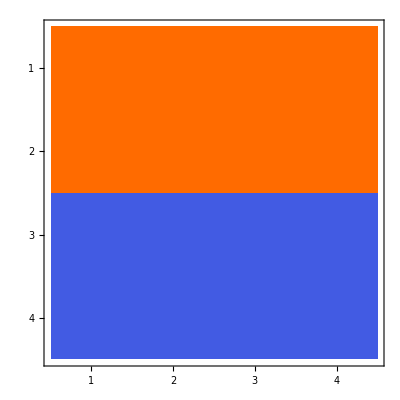
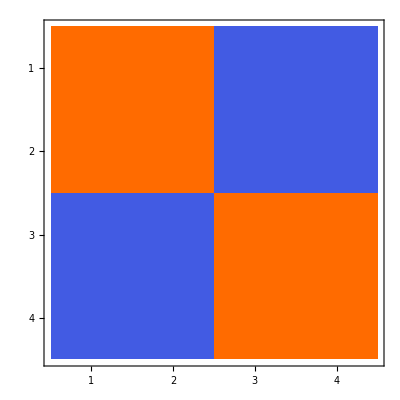
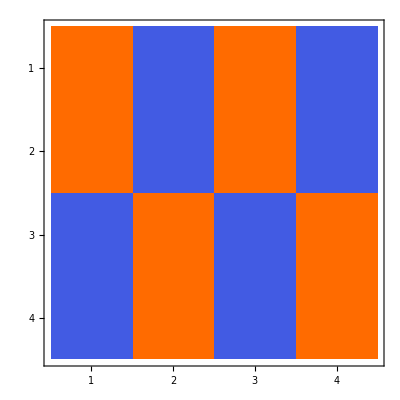
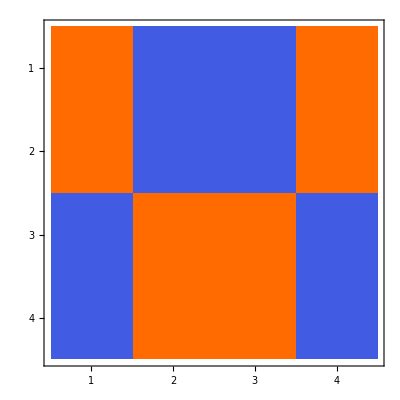

```mathematica
MatrixPlot[#[[;;,;;]]]&/@(2a-ConstantArray[1,{16,4,4}])
```

```mathematica
Binomial[7,4]
```

35

```mathematica
Binomial[31,16]
```

300540195

```mathematica
ind=Subsets[{2,3,4},{2}];
```

```mathematica
a[[3]]
```

{{1,0,1,0},{1,0,1,0},{1,0,1,0},{1,0,1,0}}

```mathematica
ReplacePart[a[[3]],{{_,3}->0,{_,4}->1}]
```

{{1,0,0,1},{1,0,0,1},{1,0,0,1},{1,0,0,1}}

```mathematica
b=DeleteDuplicates[Flatten[Table[ReplacePart[#,{{_,ind[[i,1]]}->0,{_,ind[[i,2]]}->0}],{i,3}]&/@a,1]][[4;;]];
```

```mathematica
b=Join[b,DeleteDuplicates[Flatten[Table[ReplacePart[#,{ind[[i,1]]->{0,0,0,0},ind[[i,2]]->{0,0,0,0}}],{i,3}]&/@a,1]][[4;;]]];
```

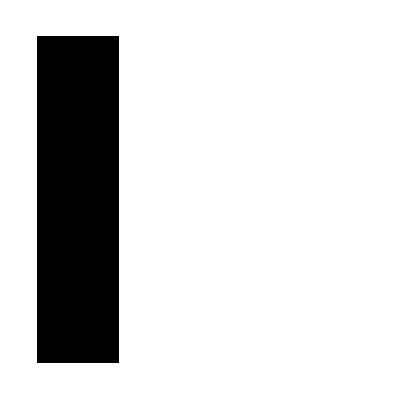
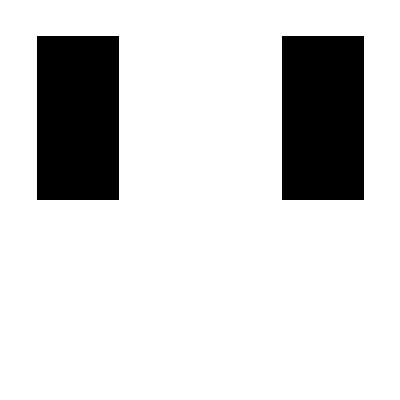
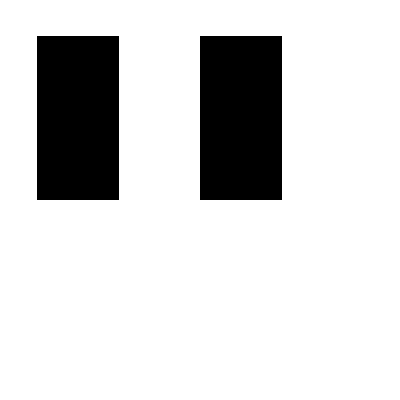
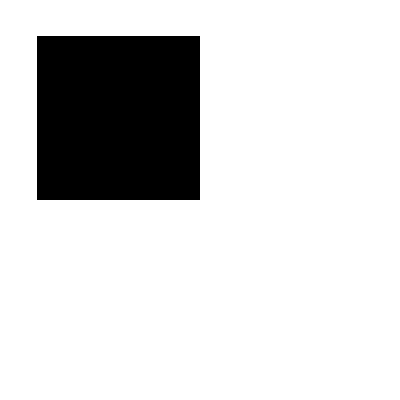
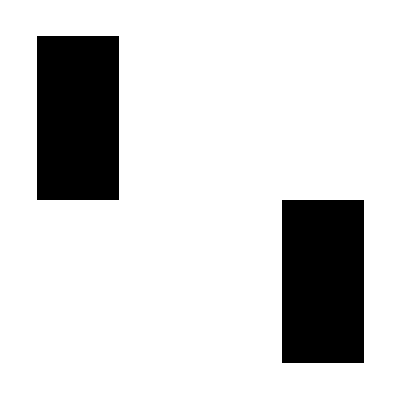
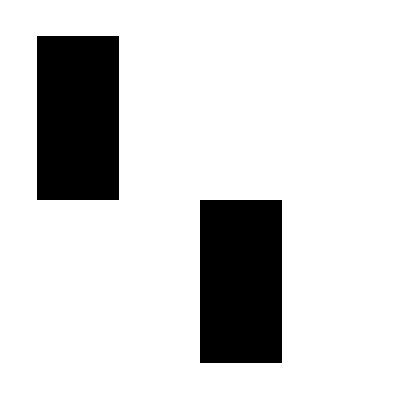
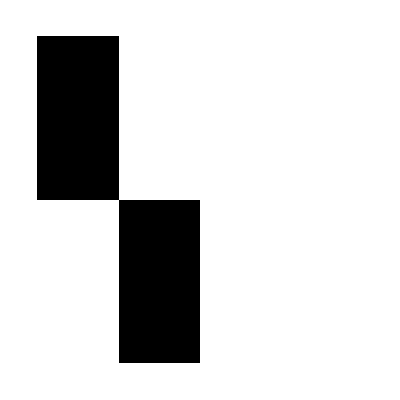
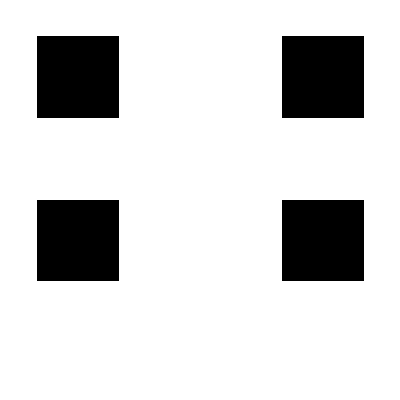

```mathematica
ArrayPlot/@DeleteDuplicates[b]
```

```mathematica
Normal[SparseArray[{{1,1},{2,2},{2,3},{1,4}}->{1,1,-1,-1},{4,4}]]
If[column[[1]].column[[4]]==-1∧column[[2]].column[[3]]==-1,]
```

```mathematica
Normal[SparseArray[{{1,1},{2,2},{2,3},{1,4}}->{1,1,-1,-1},{4,4}]][[;;,2]].Normal[SparseArray[{{1,1},{2,2},{2,3},{1,4}}->{1,1,-1,-1},{4,4}]][[;;,3]]
```

-1

```mathematica
Binomial[7,1]
```

7

```mathematica
Tuples[Range[15]+1,2][[1;;10]]
```

{{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11}}

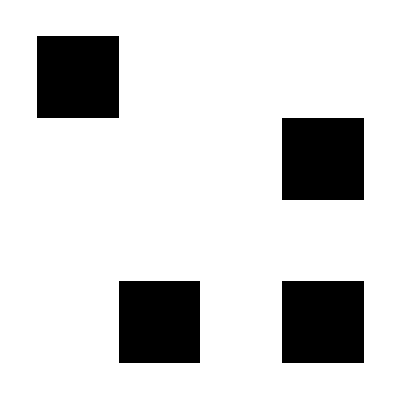

```mathematica
(A=Normal[SparseArray[{{1,1},{4,2},{2,4},{4,4}}->{1,1,1,1},{4,4}]])//ArrayPlot
```

```mathematica
A//Transpose//ArrayPlot
```

-Graphics-

```mathematica
ThreeQ={};
Do[
cube=ArrayReshape[KroneckerProduct[qubit1[[j]],a[[i]]],{4,4,4}]+ArrayReshape[KroneckerProduct[{1,1,1,1}-qubit1[[j]],ConstantArray[1,{4,4}]-a[[i]]],{4,4,4}];
AppendTo[ThreeQ,cube]
,{i,1,16},{j,1,4}]
```

## Forma correcta de exportar

```mathematica
Export["/home/jadeleon/Documents/component-erasing-maps/results/3qubits.dat",ThreeQ,"List"]
```

/home/jadeleon/Documents/component-erasing-maps/results/3qubits.dat

```mathematica
ThreeQ=ToExpression[Import["/home/jadeleon/Documents/component-erasing-maps/results/3qubits.dat","List"]];
```

```mathematica
Cube3q[ThreeQ[[3]]//Flatten]
```

-Graphics3D-

```mathematica
FourQ={};
Do[
hyperCube=((ArrayReshape[KroneckerProduct[qubit1[[i]],ThreeQ[[j]]],{4,4,4,4}]+ArrayReshape[KroneckerProduct[{1,1,1,1}-qubit1[[i]],ConstantArray[1,{4,4,4}]-ThreeQ[[j]]],{4,4,4,4}])//Flatten);
AppendTo[FourQ,hyperCube]
,{i,1,4},{j,1,64}]
```

```mathematica
AllTrue[(PCE[#]//Reshuffle//PTest)&/@FourQ,TrueQ]
```

True

```mathematica
Export["/home/jadeleon/Documents/component-erasing-maps/results/4qubits.dat",FourQ]
```

/home/jadeleon/Documents/component-erasing-maps/results/4qubits.dat

```mathematica
(PCE[#//Flatten]//Reshuffle//PTest)&/@ThreeQ
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
AllTrue[{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},TrueQ]
```

True

```mathematica
Cube3q[Position[#,1]-1]&/@ThreeQ
```

## 3 qubits

```mathematica
ind
```

{{2,3},{2,4},{3,4}}

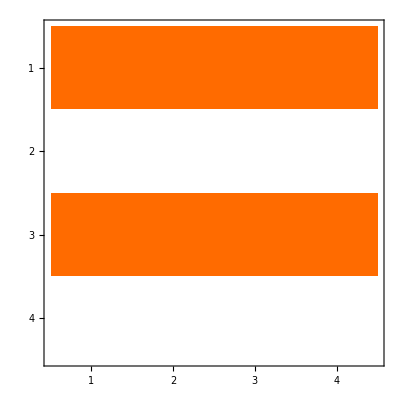
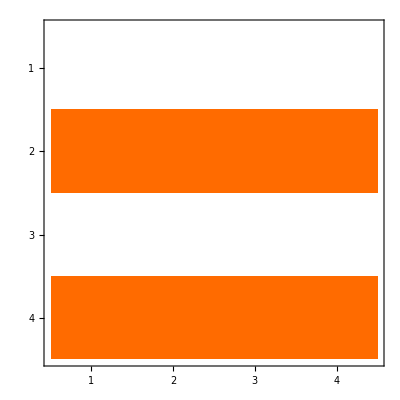
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@ThreeQ[[34]]
```

```mathematica
MatrixPlot/@ReplacePart[ThreeQ[[34]],2->ConstantArray[0,{4,4}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

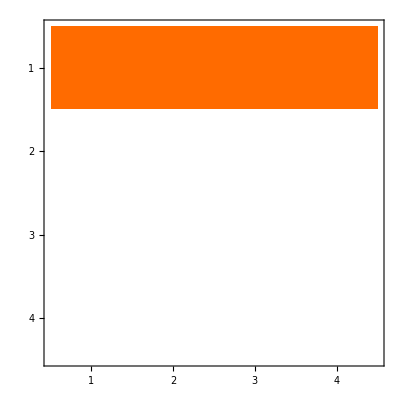
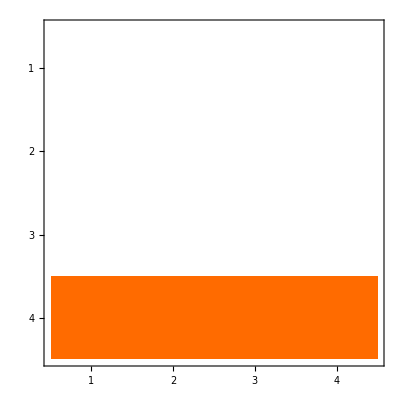
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@ReplacePart[ThreeQ[[34]],{{_,2,_}->0,{_,3,_}->0}]
```

```mathematica
MatrixPlot/@ThreeQ[[4;;5]][[1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
64*9
```

576

```mathematica
q3c16=DeleteDuplicates[Flatten[Table[ReplacePart[#,Borrado[3][[i]]]&/@ThreeQ,{i,Length[Borrado[3]]}],1]];q3c16//Length
```

255

```mathematica
AllTrue[(PCE[#//Flatten]//Reshuffle//PTest)&/@q3c16,TrueQ]
```

True

```mathematica
q3c16=DeleteDuplicates[Flatten[Table[ReplacePart[#,Borrado[3][[i]]]&/@ThreeQ,{i,Length[Borrado[3]]}],1]];q3c16//Length;
list=q3c16;q3c16={};
(If[Count[#//Flatten,1]==16,AppendTo[q3c16,#],Nothing])&/@list;
```

```mathematica
q3c16//Length
```

246

```mathematica
Cube3q[ReplacePart[ThreeQ[[1]],#]//Flatten]&/@comb1
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
evenper[x_]:=Select[Permutations[x],Signature[#]==1&]
```

```mathematica
oddper[x_]:=Select[Permutations[x],Signature[#]==-1&]
```

```mathematica
Signature[Permutations[{1,2,3}][[2]]]
```

-1

```mathematica
Cube3q[ReplacePart[SparseArray[{{1,1,1},{4,4,4},{1,1,4},{4,4,1},{1,4,1},{4,1,1},{4,1,4},{1,4,4}}->ConstantArray[1,8],{4,4,4}]//Normal,#]//Flatten]&/@comb
```

```mathematica
rows=Table[#->0&/@evenper[{1,i,_}],{i,2,4}]//Transpose
```

{{{1,2,_}→0,{1,3,_}→0,{1,4,_}→0},{{2,_,1}→0,{3,_,1}→0,{4,_,1}→0},{{_,1,2}→0,{_,1,3}→0,{_,1,4}→0}}

```mathematica
columns=Permutations[Table[#->0&/@oddper[{1,_,i}],{i,2,4}]//Transpose][[5]]
```

{{{2,1,_}→0,{3,1,_}→0,{4,1,_}→0},{{1,_,2}→0,{1,_,3}→0,{1,_,4}→0},{{_,2,1}→0,{_,3,1}→0,{_,4,1}→0}}

```mathematica
Permutations[{1,2,3}]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
comb1={};
Do[
AppendTo[comb1,Join[columns[[i]],rows[[i]]]]
,{i,3}]
```

```mathematica
comb=Delete[comb,{{3},{5},{6}}]
```

{{{1,2,_}→0,{1,3,_}→0,{1,4,_}→0,{_,1,2}→0,{_,1,3}→0,{_,1,4}→0},{{1,2,_}→0,{1,3,_}→0,{1,4,_}→0,{2,_,1}→0,{3,_,1}→0,{4,_,1}→0},{{_,1,2}→0,{_,1,3}→0,{_,1,4}→0,{2,_,1}→0,{3,_,1}→0,{4,_,1}→0}}

```mathematica
Delete[comb1,{{3},{5},{6}}]
```

{{{1,2,_}→0,{1,3,_}→0,{1,4,_}→0,{2,_,1}→0,{3,_,1}→0,{4,_,1}→0},{{1,2,_}→0,{1,3,_}→0,{1,4,_}→0,{_,1,2}→0,{_,1,3}→0,{_,1,4}→0},{{2,_,1}→0,{3,_,1}→0,{4,_,1}→0,{_,1,2}→0,{_,1,3}→0,{_,1,4}→0}}

```mathematica
Cube3q[ReplacePart[ThreeQ[[1]],{{1,_,2}->0,{1,_,3}->0,{1,_,4}->0}]//Flatten]
```

-Graphics3D-

```mathematica
Borrado[qubits_]:=Module[{ind},
ind=Subsets[{2,3,4},{2}];
Flatten[Table[{ReplacePart[ConstantArray[_,qubits],j->ind[[i,1]]]->0,ReplacePart[ConstantArray[_,qubits],j->ind[[i,2]]]->0},{i,3},{j,qubits}],1]
]
```

```mathematica
FindNextCase[Current_List,componentsErased_Integer]:=Module[{indices,all,repeated,dim,notRepeated,qubits},
qubits=Length[Dimensions[Current][[2;;]]];
indices=Borrado[qubits];
all=Flatten[Table[ReplacePart[#,indices[[i]]]&/@Current,{i,Length[indices]}],1];
repeated=If[Count[#//Flatten,1]==componentsErased,#,Nothing]&/@all;
notRepeated=DeleteDuplicates[ArrayReshape[repeated,{Length[repeated],Power[4,qubits]}]];
dim=Length[notRepeated];
ArrayReshape[notRepeated,Flatten[Append[{dim},ConstantArray[4,qubits]]]]
]
```

```mathematica
Dimensions[ThreeQ]
```

{64,4,4,4}

```mathematica
If[Count[#//Flatten,1]==componentsErased,#,Nothing]&/@all
```

```mathematica
DeleteDuplicates[]
```

```mathematica
FindNextCase[FindNextCase[a,4],2]//Length
```

15

```mathematica
Borrado[Length[Dimensions[ThreeQ][[2;;]]]]
```

{{{2,_,_}→0,{3,_,_}→0},{{_,2,_}→0,{_,3,_}→0},{{_,_,2}→0,{_,_,3}→0},{{2,_,_}→0,{4,_,_}→0},{{_,2,_}→0,{_,4,_}→0},{{_,_,2}→0,{_,_,4}→0},{{3,_,_}→0,{4,_,_}→0},{{_,3,_}→0,{_,4,_}→0},{{_,_,3}→0,{_,_,4}→0}}

32 componentes

```mathematica
ThreeQ//Length
```

64

16 componentes

```mathematica
c16=FindNextCase[ThreeQ,16];c16//Length
```

246

```mathematica
273-246
```

27

8 componentes

```mathematica
c8=FindNextCase[c16,8];c8//Length
```

342

4 componentes

```mathematica
c4=FindNextCase[c8,4];c4//Length
```

192

```mathematica
273-192
```

81

```mathematica
81/27
```

3

```mathematica
c4New={};
Do[
If[Count[ReplacePart[c8[[i]],#]//Flatten,1]==4,AppendTo[c4New,ReplacePart[c8[[i]],#]],Nothing]&/@comb1
,{i,Length[c8]}]
```

```mathematica
c4New2=If[(PCE[#//Flatten]//Reshuffle//PTest)==True,#,Nothing]&/@c4New;
```

```mathematica
DeleteDuplicates[Join[c4,c4New2]]//Length
```

273

```mathematica
Cube3q[#//Flatten]&/@DeleteDuplicates[Join[c4,c4New2]][[192;;200]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
{Cube3q[SparseArray[{{1,1,1},{1,1,2},{4,3,4},{4,3,3}}->ConstantArray[1,4],{4,4,4}]//Normal//Flatten],Cube3q[SparseArray[{{1,1,1},{1,1,2},{4,3,4},{4,3,3},{4,1,1},{4,1,2},{1,3,3},{1,3,4}}->ConstantArray[1,8],{4,4,4}]//Normal//Flatten],Cube3q[SparseArray[{{1,1,1},{1,1,2},{4,3,4},{4,3,3},{4,1,1},{4,1,2},{1,3,3},{1,3,4},{2,2,2},{3,2,2},{2,2,1},{3,2,1},{2,4,3},{3,4,3},{2,4,4},{3,4,4}}->ConstantArray[1,16],{4,4,4}]//Normal//Flatten]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
PCE[SparseArray[{{1,1,1},{1,1,2},{4,3,4},{4,3,3},{4,1,1},{4,1,2},{1,3,3},{1,3,4},{2,2,2},{3,2,2},{2,2,1},{3,2,1},{2,4,3},{3,4,3},{2,4,4},{3,4,4}}->ConstantArray[1,16],{4,4,4}]//Normal//Flatten]//Reshuffle//PTest
```

True

```mathematica
192+Length[c4New2]
```

534

```mathematica
c8New={};
Do[
If[Count[ReplacePart[ThreeQ[[i]],#]//Flatten,1]==16,AppendTo[c8New,ReplacePart[ThreeQ[[i]],#]],Nothing]&/@comb1
,{i,Length[ThreeQ]}]
```

```mathematica
Borrado[3]
```

{{{2,_,_}→0,{3,_,_}→0},{{_,2,_}→0,{_,3,_}→0},{{_,_,2}→0,{_,_,3}→0},{{2,_,_}→0,{4,_,_}→0},{{_,2,_}→0,{_,4,_}→0},{{_,_,2}→0,{_,_,4}→0},{{3,_,_}→0,{4,_,_}→0},{{_,3,_}→0,{_,4,_}→0},{{_,_,3}→0,{_,_,4}→0}}

```mathematica
FindNextCase[ThreeQ,16]//Length
```

246

```mathematica
Cube3q[ThreeQ[[29]]//Flatten]
```

-Graphics3D-

```mathematica
Cube3q[#//Flatten]&/@FindNextCase[{ThreeQ[[29]]},16]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Cube3q[#//Flatten]&/@DeleteDuplicates[Join[c4,c4New2]][[25;;50]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

2 componentes

```mathematica
(246-192)/27
```

2

```mathematica
Cube3q[c8[[135]]//Flatten]
PCE[c8[[135]]//Flatten]//Reshuffle//PTest
```

-Graphics3D-

True

```mathematica
diagonal=SparseArray[{{1,1,1},{4,1,4},{1,3,4},{4,3,3}}->ConstantArray[1,4],{4,4,4}]//Normal//Flatten;
Cube3q[diagonal]
PCE[diagonal]//Reshuffle//PTest
```

-Graphics3D-

False

```mathematica
onlyCorrelationsq3=Subsets[Range[27],{7}];
```

```mathematica
(onlyCorrelationsq3//Length)/1000//N
```

888.03

```mathematica
Prepend[Normal[SparseArray[onlyCorrelationsq3[[3]]->ConstantArray[1,7],{27}]],1]
```

{1,1,1,1,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
onlyCorrInd=Flatten[Table[{i,j,k},{i,2,4},{j,2,4},{k,2,4}],2];PrependTo[onlyCorrInd,{1,1,1}]
```

{{1,1,1},{2,2,2},{2,2,3},{2,2,4},{2,3,2},{2,3,3},{2,3,4},{2,4,2},{2,4,3},{2,4,4},{3,2,2},{3,2,3},{3,2,4},{3,3,2},{3,3,3},{3,3,4},{3,4,2},{3,4,3},{3,4,4},{4,2,2},{4,2,3},{4,2,4},{4,3,2},{4,3,3},{4,3,4},{4,4,2},{4,4,3},{4,4,4}}

#### Ahorita va a ir hasta 90000

```mathematica
onlyCorr={};
Do[
q=Normal[SparseArray[onlyCorrInd->Prepend[Normal[SparseArray[onlyCorrelationsq3[[i]]->ConstantArray[1,7],{27}]],1],{4,4,4}]]//Flatten;
If[(PCE[q]//Reshuffle//PTest)==True,AppendTo[onlyCorr,q],Nothing]
,{i,100,1000}]
```

```mathematica
onlyCorr
```

Nothing

```mathematica
MaxMemoryUsed[Subsets[Range[27],{7}];]
```

92439632

```mathematica
1*3600/38//N
```

94.7368

```mathematica
38*90/3600//N
```

0.95

```mathematica
sinRepetir=DeleteDuplicates[ArrayReshape[todos,{Length[todos],4^3}]];sinRepetir//Length
```

246

```mathematica
sinRepetir=ArrayReshape[sinRepetir,{Length[sinRepetir],4,4,4}];sinRepetir//Length
```

246

```mathematica
sinRepetir//Length
```

246

```mathematica
q3c16v3=FindNextCase[ThreeQ,16];q3c16v3//Length
```

246

```mathematica
q3c8v3=FindNextCase[q3c16v3,8];q3c8v3//Length
```

342

```mathematica
q3c4v3=FindNextCase[q3c8v3,4];q3c4v3//Length
```

192

```mathematica
q3c2v3=FindNextCase[q3c4v3,2];q3c2v3//Length
```

36

```mathematica
q3c1v3=FindNextCase[q3c2v3,1];q3c1v3//Length
```

1

```mathematica
PCE[SparseArray[{{1,1,1},{4,4,4},{1,1,4},{4,4,1},{1,4,1},{4,1,1},{4,1,4},{1,4,4},{1,2,2},{1,2,3},{1,3,2},{1,3,3},{4,2,2},{4,2,3},{4,3,2},{4,3,3}}->ConstantArray[1,16],{4,4,4}]//Normal//Flatten]//Reshuffle//PTest
```

True

```mathematica
{Cube3q[SparseArray[{{1,1,1},{4,4,4}}->ConstantArray[1,2],{4,4,4}]//Normal//Flatten],Cube3q[SparseArray[{{1,1,1},{4,4,4},{1,1,4},{4,4,1}}->ConstantArray[1,4],{4,4,4}]//Normal//Flatten],Cube3q[SparseArray[{{1,1,1},{4,4,4},{1,1,4},{4,4,1},{1,4,1},{4,1,1},{4,1,4},{1,4,4}}->ConstantArray[1,8],{4,4,4}]//Normal//Flatten],Cube3q[SparseArray[{{1,1,1},{4,4,4},{1,1,4},{4,4,1},{1,4,1},{4,1,1},{4,1,4},{1,4,4},{1,2,2},{1,2,3},{1,3,2},{1,3,3},{4,2,2},{4,2,3},{4,3,2},{4,3,3}}->ConstantArray[1,16],{4,4,4}]//Normal//Flatten]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
{Cube3q[SparseArray[{{1,1,1},{2,3,4}}->ConstantArray[1,2],{4,4,4}]//Normal//Flatten],Cube3q[SparseArray[{{1,1,1},{2,3,4},{1,1,4},{2,3,1}}->ConstantArray[1,4],{4,4,4}]//Normal//Flatten],Cube3q[SparseArray[{{1,1,1},{2,3,4},{1,1,4},{2,3,1},{1,3,4},{2,1,4},{1,3,1},{2,1,1}}->ConstantArray[1,8],{4,4,4}]//Normal//Flatten]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

False

```mathematica
Cube3q[ReplacePart[ConstantArray[1,{4,4,4}],{{1,_,2}->0,{1,_,3}->0}]//Flatten]
```

-Graphics3D-

```mathematica
Cube3q[ReplacePart[ConstantArray[1,{4,4,4}],{{_,2,1}->0,{_,3,1}->0}]//Flatten]
```

-Graphics3D-

```mathematica
PCE[ReplacePart[ReplacePart[ReplacePart[ThreeQ[[16]],{{2,1,_}->0,{3,1,_}->0}],{{_,2,1}->0,{_,3,1}->0}],{{1,_,2}->0,{1,_,3}->0}]//Flatten]
```

False

```mathematica
Cube3q[#//Flatten]&/@ThreeQ[[16;;30]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
p1=Flatten[Table[ReplacePart[#,indices[[i]]]&/@{ThreeQ[[35]]},{i,Length[indices]}],1][[3]];
```

```mathematica
Cube3q[#//Flatten]&/@Flatten[Table[ReplacePart[#,indices[[i]]]&/@{ThreeQ[[30]]},{i,Length[indices]}],1]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Cube3q[#//Flatten]&/@FindNextCase[{ThreeQ[[2]]},16]
```

```mathematica
{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}
```

```mathematica
Cube3q[#//Flatten]&/@q3c8v3[[1;;10]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
FindNextCase[{ThreeQ[[45]]},16]
```

{{{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}}},{{{1,0,0,1},{0,0,0,0},{0,0,0,0},{0,1,1,0}},{{1,0,0,1},{0,0,0,0},{0,0,0,0},{0,1,1,0}},{{1,0,0,1},{0,0,0,0},{0,0,0,0},{0,1,1,0}},{{1,0,0,1},{0,0,0,0},{0,0,0,0},{0,1,1,0}}},{{{1,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,0,0}},{{1,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,0,0}},{{1,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,0,0}},{{1,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,0,0}}},{{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{1,0,0,0},{0,0,1,0},{1,0,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,1,0},{1,0,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,1,0},{1,0,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,1,0},{1,0,0,0},{0,0,1,0}}},{{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}},{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{1,0,0,1},{0,1,1,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,1},{0,1,1,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,1},{0,1,1,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,1},{0,1,1,0},{0,0,0,0},{0,0,0,0}}},{{{1,0,0,0},{0,1,0,0},{1,0,0,0},{0,1,0,0}},{{1,0,0,0},{0,1,0,0},{1,0,0,0},{0,1,0,0}},{{1,0,0,0},{0,1,0,0},{1,0,0,0},{0,1,0,0}},{{1,0,0,0},{0,1,0,0},{1,0,0,0},{0,1,0,0}}}}

```mathematica
FindNextCase[{ThreeQ[[45]]},16]
```

{{{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}}},{{{1,0,0,1},{0,0,0,0},{0,0,0,0},{0,1,1,0}},{{1,0,0,1},{0,0,0,0},{0,0,0,0},{0,1,1,0}},{{1,0,0,1},{0,0,0,0},{0,0,0,0},{0,1,1,0}},{{1,0,0,1},{0,0,0,0},{0,0,0,0},{0,1,1,0}}},{{{1,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,0,0}},{{1,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,0,0}},{{1,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,0,0}},{{1,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,0,0}}},{{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{1,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,0,0}},{{1,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,0,0}},{{1,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,0,0}},{{1,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,0,0}}},{{{1,0,0,0},{0,0,1,0},{1,0,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,1,0},{1,0,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,1,0},{1,0,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,1,0},{1,0,0,0},{0,0,1,0}}},{{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}},{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{1,0,0,1},{0,1,1,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,1},{0,1,1,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,1},{0,1,1,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,1},{0,1,1,0},{0,0,0,0},{0,0,0,0}}},{{{1,0,0,0},{0,1,0,0},{1,0,0,0},{0,1,0,0}},{{1,0,0,0},{0,1,0,0},{1,0,0,0},{0,1,0,0}},{{1,0,0,0},{0,1,0,0},{1,0,0,0},{0,1,0,0}},{{1,0,0,0},{0,1,0,0},{1,0,0,0},{0,1,0,0}}}}

```mathematica
Cube3q[#//Flatten]&/@FindNextCase[{ThreeQ[[45]]},16]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
c2=FindNextCase[c4,2];c2//Length
```

36

```mathematica
Cube3q[#//Flatten]&/@c2
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

1 componente

```mathematica
q3c1V2=FindNextCase[q3c2V2,1];q3c1V2//Length
```

1

#### 8 componentes

```mathematica
q3c8=DeleteDuplicates[Flatten[Table[ReplacePart[#,indices[[i]]]&/@q3c16,{i,Length[indices]}],1]];q3c8//Length
```

597

```mathematica
AllTrue[(PCE[#//Flatten]//Reshuffle//PTest)&/@q3c8,TrueQ]
```

True

```mathematica
q3c8New=If[Tally[#//Flatten][[1,2]]==8,#,Nothing]&/@q3c8;q3c8New//Length
```

342

```mathematica
AllTrue[If[Tally[#//Flatten][[1,2]]==8,True,Nothing]&/@q3c8New,TrueQ]
```

True

```mathematica
q3c8=q3c8New;
```

```mathematica
Cube3q[q3c8New[[17]]//Flatten]
```

-Graphics3D-

#### 4 componentes

```mathematica
q3c4=DeleteDuplicates[Flatten[Table[ReplacePart[#,indices[[i]]]&/@q3c8,{i,Length[indices]}],1]];q3c4//Length
```

534

```mathematica
q3c4New=If[Tally[#//Flatten][[1,2]]==4,#,Nothing]&/@q3c4;q3c4New//Length
```

192

```mathematica
q3c4=q3c4New;
```

```mathematica
Cube3q[q3c4[[130]]//Flatten]
```

-Graphics3D-

```mathematica
AllTrue[(PCE[#//Flatten]//Reshuffle//PTest)&/@q3c4,TrueQ]
```

True

## Otros

```mathematica
id=PCE[{1,1,0,0}]//Reshuffle//Eigenvectors;PCE[{1,1,0,0}]//Reshuffle//Eigenvalues
Dirac[#]&/@id
id=PCE[{1,0,1,0}]//Reshuffle//Eigenvectors;PCE[{1,0,1,0}]//Reshuffle//Eigenvalues
Dirac[#]&/@id
id=PCE[{1,0,0,1}]//Reshuffle//Eigenvectors;PCE[{1,0,0,1}]//Reshuffle//Eigenvalues
Dirac[#]&/@id
```

{1/2,1/2,0,0}

{00+11,01+10,-00+11,-01+10}

{1/2,1/2,0,0}

{00+11,-01+10,-00+11,01+10}

{1/2,1/2,0,0}

{11,00,10,01}

```mathematica
id=PCE[{1,0,1,1}]//Reshuffle//Eigensystem
PCE[{1,0,1,1}]//Reshuffle//Eigenvalues
Dirac[#]&/@id[[2]]
```

{{3/4,-1/4,1/4,1/4},{{1,0,0,1},{0,1,1,0},{-1,0,0,1},{0,-1,1,0}}}

{3/4,-1/4,1/4,1/4}

{00+11,01+10,-00+11,-01+10}

```mathematica
(PCE[{1,0,1,1}]//Reshuffle).{0,1,1,0}
```

{0,-1/4,-1/4,0}

```mathematica
PCE[Flatten[KroneckerProduct[{1,0,0,0},{1,0,0,0}]]]//Reshuffle//Eigenvectors
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Dirac[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}]
```

1111

```mathematica
$Assumptions=And@@Flatten[Table[Subscript[r, i,j]==1,{i,0,3},{j,0,3}]]
```

r_(0,0)==1&&r_(0,1)==1&&r_(0,2)==1&&r_(0,3)==1&&r_(1,0)==1&&r_(1,1)==1&&r_(1,2)==1&&r_(1,3)==1&&r_(2,0)==1&&r_(2,1)==1&&r_(2,2)==1&&r_(2,3)==1&&r_(3,0)==1&&r_(3,1)==1&&r_(3,2)==1&&r_(3,3)==1

```mathematica
(#//FullSimplify)&/@eigen
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
List@@(1+Subscript[r, 0,1]-Subscript[r, 0,2]-Subscript[r, 0,3]+Subscript[r, 1,0]+Subscript[r, 1,1]-Subscript[r, 1,2]-Subscript[r, 1,3]-Subscript[r, 2,0]-Subscript[r, 2,1]+Subscript[r, 2,2]+Subscript[r, 2,3]-Subscript[r, 3,0]-Subscript[r, 3,1]+Subscript[r, 3,2]+Subscript[r, 3,3])
```

{1,r_(0,1),-r_(0,2),-r_(0,3),r_(1,0),r_(1,1),-r_(1,2),-r_(1,3),-r_(2,0),-r_(2,1),r_(2,2),r_(2,3),-r_(3,0),-r_(3,1),r_(3,2),r_(3,3)}

```mathematica
List@@(Expand[1/16 (1+Subscript[r, 0,1]-Subscript[r, 0,2]-Subscript[r, 0,3]+Subscript[r, 1,0]+Subscript[r, 1,1]-Subscript[r, 1,2]-Subscript[r, 1,3]-Subscript[r, 2,0]-Subscript[r, 2,1]+Subscript[r, 2,2]+Subscript[r, 2,3]-Subscript[r, 3,0]-Subscript[r, 3,1]+Subscript[r, 3,2]+Subscript[r, 3,3])])
```

{1/16,(r_(0,1))/16,-(r_(0,2))/16,-(r_(0,3))/16,(r_(1,0))/16,(r_(1,1))/16,-(r_(1,2))/16,-(r_(1,3))/16,-(r_(2,0))/16,-(r_(2,1))/16,(r_(2,2))/16,(r_(2,3))/16,-(r_(3,0))/16,-(r_(3,1))/16,(r_(3,2))/16,(r_(3,3))/16}

```mathematica
Subscript[r, 0,0,0]=1;a=PCE[Table[Subscript[r, i,j,k],{i,0,3},{j,0,3},{k,0,3}]//Flatten]//Reshuffle;
```

```mathematica
a//MatrixForm
```

```mathematica
PrincipalMinors[mat_,r_]:=DeleteDuplicates[Flatten[Diagonal[Map[Reverse,Minors[mat,#],{0,1}]]&/@r]];
```

```mathematica
PrincipalMinors[a,{1}]//Expand//FullSimplify//TableForm
```

1/64 (1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))
1/64 (1-r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3))
1/64 (1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3))
1/64 (1-r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3))
1/64 (1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)-r_(3,3,0)-r_(3,3,3))
1/64 (1-r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3))
1/64 (1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3))
1/64 (1-r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3))

```mathematica
Subscript[r, 0,0]=1;Flatten[Table[Subscript[r, i,j],{i,0,3},{j,0,3}]]
```

{1,r_(0,1),r_(0,2),r_(0,3),r_(1,0),r_(1,1),r_(1,2),r_(1,3),r_(2,0),r_(2,1),r_(2,2),r_(2,3),r_(3,0),r_(3,1),r_(3,2),r_(3,3)}

```mathematica
PCE[Flatten[KroneckerProduct[{1,0,0,1},{1,0,0,1}]]]//Reshuffle//Eigenvalues//Tally
```

{{1/4,4},{0,12}}